# CO2 Phase Diagram

## PC-SAFT (Perturbed-Chain Statistical Associating Fluid Theory)

Andy Ylitalo, with guidance from Dr. Huikuan Chao and mentorship from Prof. Zhen-Gang Wang

## Questions

## 0. Setup

```mathematica
SetDirectory[FileNameJoin[{"C:","Users","Andy.DESKTOP-CFRG05F","OneDrive - California Institute of Technology", "Documents", "Research", "Wang", "PC-SAFT"}]];
```

## 1. Equations

```mathematica
d[σ_,β_,ϵ_]:=σ(1-0.12Exp[-3ϵ β]);  (* temperature-dependent particle diameter, Gross and Sadowski (2001) *)
```

### Free energy of ideal gas

```mathematica
βfIG[ρ_, N_:2]:= ρ/N(Log[ρ /N ]-1);
```

### Free energy of hard-sphere liquid

Note that ξ[ρ,σ,3] represents the total packing fraction and is therefore dimensionless. In general, ξ[ρ,σ,n] has dimensions of (length)^(n-3).

```mathematica
ξ[ρ_,d_,j_]:=π/6 ρ d^j;
```

```mathematica
βfHS[ρ_,d_]:=6/π( (3 ξ[ρ,d,1]ξ[ρ,d,2])/(1-ξ[ρ,d,3])
+ (ξ[ρ,d,2])^3/(ξ[ρ,d,3](1-ξ[ρ,d,3])^2)
+ ((ξ[ρ,d,2])^3/(ξ[ρ,d,3])^2-ξ[ρ,d,0])Log[1-ξ[ρ,d,3]] );
```

### Free energy of association

```mathematica
gii[ρ_,d_]:=1/(1-ξ[ρ,d,3])+ 3ξ[ρ,d,2] d/ (2(1-ξ[ρ,d,3])^2)+ (ξ[ρ,d,2])^2d^2 / (2(1-ξ[ρ,d,3])^3); (* radial pair distribution function for segments of component i in the hard-sphere system *)
```

```mathematica
βfAssoc[ρ_,d_,N_:2]:=-(N-1)/N ρ Log[gii[ρ,d]];
```

### Free energy of dispersion

First, load the constants for the polynomial approximation of the integrals I1 and I2 in Gross and Sadowski (2001). We refer to them here as J1 and J2 according to the nomenclature used by Xu et al. (2012).

```mathematica
JConstants=Import[FileNameJoin[{"Data","J_integral_const_a_b.csv"}]];
```

```mathematica
a0=JConstants[[2;;-1, 2]];
a1 = JConstants[[2;;-1, 3]];
a2 = JConstants[[2;;-1, 4]];
b0 = JConstants[[2;;-1, 5]];
b1 = JConstants[[2;;-1, 6]];
b2 = JConstants[[2;;-1, 7]];
```

```mathematica
a= a0 +  a1/2 ; (* full formula: a = a0 + (N-1)/N a1 + (N-1)/N (N-2)/N a2 *)
b= b0 +  b1/2 ; (* full formula: b = b0 + (N-1)/N b1 + (N-1)/N (N-2)/N b2 *)
```

```mathematica
J1[ρ_,d_,N_]:=Sum[a[[i]](ξ[ρ,d,3])^(i-1),{i,1,Length[a]}]
J2[ρ_,d_,N_]:=Sum[b[[i]](ξ[ρ,d,3])^(i-1),{i,1,Length[a]}]
```

```mathematica
M[ρ_,d_,N_:2]:=1+N(8 ξ[ρ,d,3] - 2 (ξ[ρ,d,3])^2)/(1-ξ[ρ,d,3])^4+ (1-N)(20 ξ[ρ,d,3] - 27(ξ[ρ,d,3])^2 + 12 (ξ[ρ,d,3])^3 - 2(ξ[ρ,d,3])^4)/((1-ξ[ρ,d,3])^2(2-ξ[ρ,d,3])^2); (* dimensionless--might be a typo (compare eqn 25 of Gross and Sadowski and the eqn for M below eqn 6 in Xu et al *)
```

```mathematica
βfDisp[ρ_,σ_,β_,ϵ_,N_:2]:=-π ρ^2 (2 J1[ρ,d[σ,β,ϵ],N] β ϵ + N (M[ρ,d[σ,β,ϵ],N] )^(-1)J2[ρ,d[σ,β,ϵ],N] (β ϵ)^2) σ^3;
```

### Total Free Energy

```mathematica
βf[ρ_,σ_,β_,ϵ_,N_:2]:=βfIG[ρ]+βfHS[ρ,d[σ,β,ϵ]]+βfAssoc[ρ,d[σ,β,ϵ],N]+βfDisp[ρ,σ,β,ϵ,N];
```

### Chemical potential

```mathematica
βμ[ρ_,σ_,β_,ϵ_,N_:2]:=D[βf[ρprime,σ,β,ϵ,N],ρprime]/.ρprime->ρ;
```

### Pressure

```mathematica
βp[ρ_,σ_,β_,ϵ_]:= -βf[ρ,σ,β,ϵ]+ρ βμ[ρ,σ,β,ϵ];
```

## 2. Plot

```mathematica
T=290; (* temperature [K] *)
βParam=1/T; (* beta parameter *)
ϵCO2=170.5 ; (* attractive well depth, from Xu et al. 2012 JCP [J] *)
σCO2=1; (* bead size [σCO2] *)
dCO2 = σCO2*(1-0.12*Exp[-3ϵCO2*βParam]); (* temperature-dependent particle diameter, Gross and Sadowski (2001) *)
ρmin=0; (* minimum mass density to plot[molecules/σ^3] *)
ρmax = 0.5; (* maximum mass density to plot [molecules/σ^3] *)
```

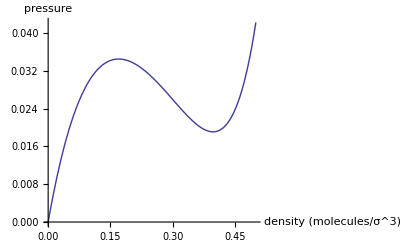

```mathematica
Plot[βp[ρ,σCO2,βParam,ϵCO2],{ρ,ρmin, ρmax},AxesLabel->{"density (molecules/σ^3)","pressure"}]
```

This plot matches the plot from Huikuan’s model (which he is confident in).